#### This code is part of the Ph.D. thesis of William Gabriel Carreras Oropesa for the São Paulo University.

```mathematica
SetAttributes[{A,B,U,T,Δ},Constant]
```

For nematogens and dipolar nanoparticles we will consider the elements of the main diagonal as a column vector:

```mathematica
Θ:=1/2{{2,-1,-1},{2,-1,-1},{-1,2,-1},{-1,2,-1},{-1,-1,2},{-1,- 1,2}};
Ω:=1/2{{2,-1-Δ,-1+Δ},{2,-1+Δ,-1-Δ},{-1-Δ,2,-1+Δ},{-1+Δ,2,-1-Δ},{-1-Δ,-1+Δ,2},{-1+Δ,-1-Δ,2}};
```

The orientational order parameters will be given as column vectors:

```mathematica
Q:=-1/2{S+η,S-η,-2 S};
X:=-1/2{R+ζ,R-ζ,-2 R};
```

```mathematica
(*Problem in the limit of ϕ=1, only the LC host*)
```

```mathematica
ξ1[S_,η_]=∑_(i=1)^6 ⅇ^((1/T) A Q.Ω[[i]]);
```

Mean field equation

```mathematica
EqS1=S==FullSimplify[1/ξ1[S,η]∑_(i=1)^6 Ω[[i,3]] ⅇ^((1/T) A Q.Ω[[i]])]/.{S->S1,T->T1,η->0}(*1*)
Eqη1=1==FullSimplify[CoefficientList[Series[1/ξ1[S,η]∑_(i=1)^6 (Ω[[i,2]]-Ω[[i,1]])ⅇ^((1/T) A Q.Ω[[i]]),{η,0,1}],η][[2]]/.{S->S1,T->T1}](*2*)
```

S1==(-2+4 ⅇ^((3 A S1 (3+Δ))/(4 T1))+2 ⅇ^((3 A S1 Δ)/(2 T1)) (-1+Δ)-2 Δ)/(2 (2+2 ⅇ^((3 A S1 Δ)/(2 T1))+2 ⅇ^((3 A S1 (3+Δ))/(4 T1))))

1==(A ((-3+Δ)^2+4 ⅇ^((3 A S1 (3+Δ))/(4 T1)) Δ^2+ⅇ^((3 A S1 Δ)/(2 T1)) (3+Δ)^2))/(8 (1+ⅇ^((3 A S1 Δ)/(2 T1))+ⅇ^((3 A S1 (3+Δ))/(4 T1))) T1)

```mathematica
(*
These equations represent the behavior of the second-order line just at the point ϕ=1 these equations will be used to determine the relationship δT/δϕ. In what follows we consider the problem with ϕ=1-δϕ, S=S1+δS, R=δR, η=0, ζ=0,T=T1+δT, donde δϕ,δS,δR,δT<<1.
*)
```

Mean field equations

```mathematica
EqS=S-Simplify[ϕ(∑_(i=1)^6 Ω[[i,3]] ⅇ^((1/T)(B X+A Q).Ω[[i]]))/(∑_(i=1)^6 ⅇ^((1/T)(B X+A Q).Ω[[i]]))];
Eqη=η-Simplify[ϕ(∑_(i=1)^6 (Ω[[i,2]]-Ω[[i,1]])ⅇ^((1/T)(B X+A Q).Ω[[i]]))/(∑_(i=1)^6 ⅇ^((1/T)(B X+A Q).Ω[[i]]))];
EqR=R-Simplify[(1-ϕ)(∑_(i=1)^6 Θ[[i,3]] ⅇ^((1/T) B Q.Θ[[i]]))/(∑_(i=1)^6 ⅇ^((1/T) B Q.Θ[[i]]))];
Eqζ=ζ-Simplify[(1-ϕ)(∑_(i=1)^6 (Θ[[i,2]]-Θ[[i,1]])ⅇ^((1/T) B Q.Θ[[i]]))/(∑_(i=1)^6 ⅇ^((1/T) B Q.Θ[[i]]))];
```

```mathematica
MyEqS=EqS/.{S->S1+δS,R->δR,η->0,ζ->0,ϕ->1-δϕ,T->T1+δT};
ExpS=Normal[Series[MyEqS,{δS,0,1},{δR,0,1},{δϕ,0,1},{δT,0,1}]];
```

```mathematica
(*We have that coeffS0+coeffS1*δS+coeffS2*δR+coeffS3*δϕ+coeffS4*δT=0*)
```

```mathematica
coeffS0x=CoefficientList[ExpS,δS][[1]]/.{δR->0,δϕ->0,δT->0}
```

S1-(4 ⅇ^((3 A S1)/(2 T1))+2 ⅇ^((3 A S1 (-1+Δ))/(4 T1)) (-1+Δ)-2 ⅇ^(-(3 A S1 (1+Δ))/(4 T1)) (1+Δ))/(2 (2 ⅇ^((3 A S1)/(2 T1))+2 ⅇ^((3 A S1 (-1+Δ))/(4 T1))+2 ⅇ^(-(3 A S1 (1+Δ))/(4 T1))))

```mathematica
coeffS1x=FullSimplify[CoefficientList[ExpS,δS][[2]]/.{δR->0,δϕ->0,δT->0}]
```

1+(3 A (-ⅇ^((9 A S1 (1+Δ))/(4 T1)) (-3+Δ)^2-4 ⅇ^((3 A S1 Δ)/(2 T1)) Δ^2-ⅇ^((3 A S1 (3+Δ))/(4 T1)) (3+Δ)^2))/(8 (1+ⅇ^((3 A S1 Δ)/(2 T1))+ⅇ^((3 A S1 (3+Δ))/(4 T1)))^2 T1)

```mathematica
coeffS2x=Simplify[CoefficientList[ExpS,δR][[2]]/.{δS->0,δϕ->0,δT->0}]
```

-(3 B ⅇ^((3 A S1 (1+Δ))/(4 T1)) (ⅇ^((3 A S1 (1+Δ))/(2 T1)) (-3+Δ)^2+4 ⅇ^((3 A S1 (-1+Δ))/(4 T1)) Δ^2+ⅇ^((3 A S1)/(2 T1)) (3+Δ)^2))/(8 (1+ⅇ^((3 A S1 Δ)/(2 T1))+ⅇ^((3 A S1 (3+Δ))/(4 T1)))^2 T1)

```mathematica
coeffS3x=Simplify[CoefficientList[ExpS,δϕ][[2]]/.{δS->0,δR->0,δT->0}]
```

(-1+2 ⅇ^((3 A S1 (3+Δ))/(4 T1))+ⅇ^((3 A S1 Δ)/(2 T1)) (-1+Δ)-Δ)/(2 (1+ⅇ^((3 A S1 Δ)/(2 T1))+ⅇ^((3 A S1 (3+Δ))/(4 T1))))

```mathematica
coeffS4x=Simplify[CoefficientList[ExpS,δT][[2]]/.{δS->0,δR->0,δϕ->0}]
```

(3 A ⅇ^((3 A S1 (1+Δ))/(4 T1)) S1 (ⅇ^((3 A S1 (1+Δ))/(2 T1)) (-3+Δ)^2+4 ⅇ^((3 A S1 (-1+Δ))/(4 T1)) Δ^2+ⅇ^((3 A S1)/(2 T1)) (3+Δ)^2))/(8 (1+ⅇ^((3 A S1 Δ)/(2 T1))+ⅇ^((3 A S1 (3+Δ))/(4 T1)))^2 T1^2)

```mathematica
(*Before continuing let's simplify these coefficients using (1) and (2)*)
```

```mathematica
coeffS0=0;(*as consequence of (1)*)
coeffS1=coeffS1x;
coeffS2=coeffS2x;
coeffS3=S1;(*as consequence of (1)*)
coeffS4=coeffS4x;
```

```mathematica
MyEqR=EqR/.{S->S1+δS,R->δR,η->0,ζ->0,ϕ->1-δϕ,T->T1+δT};
ExpR=Normal[Series[MyEqR,{δS,0,1},{δR,0,1},{δϕ,0,1},{δT,0,1}]];
```

```mathematica
(*we have that coeffR0+coeffR1*δS+coeffR2*δR+coeffR3*δϕ+coeffR4*δT=0*)
```

```mathematica
coeffR0=CoefficientList[ExpR,δS][[1]]/.{δR->0,δϕ->0,δT->0}
```

0

```mathematica
coeffR1=Simplify[CoefficientList[ExpR,δS][[2]]/.{δR->0,δϕ->0,δT->0}]
```

0

```mathematica
coeffR2=Simplify[CoefficientList[ExpR,δR][[2]]/.{δS->0,δϕ->0,δT->0}]
```

1

```mathematica
coeffR3=Simplify[CoefficientList[ExpR,δϕ][[2]]/.{δS->0,δR->0,δT->0}]
```

(1-ⅇ^((9 B S1)/(4 T1)))/(2+ⅇ^((9 B S1)/(4 T1)))

```mathematica
coeffR4=Simplify[CoefficientList[ExpR,δT][[2]]/.{δS->0,δR->0,δϕ->0}]
```

0

```mathematica
(*We need another equation which is given by the critical point condition where d^2 Ψ/dη^2=0. The total derivative must be understood as S=S(η),R=R(η) and ζ=ζ(η)*)
```

```mathematica
Λ[S_,R_,η_,ζ_]:=2 Exp[3/(2T) (A S+B R)]Cosh[1/(2T)( A η+B ζ) Δ]+2Exp[-3/(4T) (A(S+η)+B(R+ζ))]Cosh[3/(4T) (A(S-η/3)+B(R-ζ/3)) Δ]+2Exp[-3/(4T) (A(S-η)+B(R-ζ))]Cosh[3/(4T) (A(S+η/3)+B(R+ζ/3)) Δ];
f[S_,η_,R_,ζ_,ϕ_]:=1/3 ( (1-ϕ) Log[(1+2 R-ϕ) (-1+R-ζ+ϕ) (-1+R+ζ+ϕ)]+R Log[(-1-2 R+ϕ)^2/((-1+R-ζ+ϕ) (-1+R+ζ+ϕ))]+ζ Log[1-(2 ζ)/(-1+R+ζ+ϕ)])-ϕ Log[Λ[S,R,η,ζ]]+ϕ Log[6ϕ]-2 Log[6]
Ψ[S_,η_,R_,ζ_,ϕ_]:=A/4(3 S^2+η^2)+U/2 ϕ^2-μ ϕ+T f[S,η,R,ζ,ϕ];
```

```mathematica
eq1=Dt[D[G[S,η,R,ζ,ϕ],S]==0,η];
eq2=Dt[D[G[S,η,R,ζ,ϕ],S]==0,{η,2}];
eq3=Dt[D[G[S,η,R,ζ,ϕ],R]==0,η];
eq4=Dt[D[G[S,η,R,ζ,ϕ],R]==0,{η,2}];
eq5=Dt[D[G[S,η,R,ζ,ϕ],ϕ]==0,η];
eq6=Dt[D[G[S,η,R,ζ,ϕ],ϕ]==0,{η,2}];
eq7=Dt[D[G[S,η,R,ζ,ϕ],ζ]==0,η];
eq8=Dt[D[G[S,η,R,ζ,ϕ],ζ]==0,{η,2}];
```

```mathematica
(*Derivadas parciales segundas*)
```

Symmetries

```mathematica
symmetries={Derivative[1,0,0,0,0][G][S,η,R,ζ,ϕ]->0,Derivative[0,1,0,0,0][G][S,η,R,ζ,ϕ]->0,Derivative[0,0,1,0,0][G][S,η,R,ζ,ϕ]->0,Derivative[0,0,0,1,0][G][S,η,R,ζ,ϕ]->0,Derivative[0,0,0,0,1][G][S,η,R,ζ,ϕ]->0,Derivative[1,1,0,0,0][G][S,η,R,ζ,ϕ]->0,Derivative[1,0,0,1,0][G][S,η,R,ζ,ϕ]->0,Derivative[0,1,1,0,0][G][S,η,R,ζ,ϕ]->0,Derivative[0,1,0,0,1][G][S,η,R,ζ,ϕ]->0,Derivative[0,0,1,1,0][G][S,η,R,ζ,ϕ]->0,Derivative[0,0,0,1,1][G][S,η,R,ζ,ϕ]->0,Derivative[0,0,0,3,0][G][S,η,R,ζ,ϕ]->0,Derivative[0,3,0,0,0][G][S,η,R,ζ,ϕ]->0,Derivative[1,1,1,0,0][G][S,η,R,ζ,ϕ]->0,Derivative[1,1,0,0,1][G][S,η,R,ζ,ϕ]->0,Derivative[1,0,0,1,1][G][S,η,R,ζ,ϕ]->0,Derivative[0,0,1,1,1][G][S,η,R,ζ,ϕ]->0,Derivative[1,0,1,1,0][G][S,η,R,ζ,ϕ]->0,Derivative[0,1,1,0,1][G][S,η,R,ζ,ϕ]->0,Derivative[2,1,0,0,0][G][S,η,R,ζ,ϕ]->0,Derivative[2,0,0,1,0][G][S,η,R,ζ,ϕ]->0,Derivative[0,2,0,1,0][G][S,η,R,ζ,ϕ]->0,Derivative[0,1,2,0,0][G][S,η,R,ζ,ϕ]->0,Derivative[0,0,2,1,0][G][S,η,R,ζ,ϕ]->0,Derivative[0,1,0,2,0][G][S,η,R,ζ,ϕ]->0,Derivative[1,0,0,0,2][G][S,η,R,ζ,ϕ]->0,Derivative[0,1,0,0,2][G][S,η,R,ζ,ϕ]->0,Derivative[0,0,0,1,2][G][S,η,R,ζ,ϕ]->0};
```

```mathematica
totalD={Dt[S,η]->0,Dt[R,η]->0,Dt[ζ,η]->-(Derivative[0,1,0,1,0][G][S,η,R,ζ,ϕ])/(Derivative[0,0,0,2,0][G][S,η,R,ζ,ϕ]),Dt[ϕ,η]->0,Dt[ζ,{η,2}]->0};
```

```mathematica
f2=Dt[G[S,η,R,ζ,ϕ],{η,2}]/.Flatten[{symmetries,totalD}]
```

-((G^(0,1,0,1,0)[S,η,R,ζ,ϕ])^2)/(G^(0,0,0,2,0)[S,η,R,ζ,ϕ])+G^(0,2,0,0,0)[S,η,R,ζ,ϕ]

```mathematica
Eqη2=FullSimplify[TrigToExp[ (2 ⅇ^((9 (B R+A S))/(4 T)) (8 T^2-4 A T Δ^2 ϕ+3 B^2 Δ^2 ϕ (-1+R+ϕ))+(32 T^2-4 A T (9+Δ^2) ϕ+3 B^2 (9+Δ^2) ϕ (-1+R+ϕ)) Cosh[(3 (B R+A S) Δ)/(4 T)]+6 Δ ϕ (-4 A T+3 B^2 (-1+R+ϕ)) Sinh[(3 (B R+A S) Δ)/(4 T)])]]
```

2 ⅇ^((9 (B R+A S))/(4 T)) (8 T^2-4 A T Δ^2 ϕ+3 B^2 Δ^2 ϕ (-1+R+ϕ))+(32 T^2-4 A T (9+Δ^2) ϕ+3 B^2 (9+Δ^2) ϕ (-1+R+ϕ)) Cosh[(3 (B R+A S) Δ)/(4 T)]+6 Δ ϕ (-4 A T+3 B^2 (-1+R+ϕ)) Sinh[(3 (B R+A S) Δ)/(4 T)]

```mathematica
MyEqη2=Eqη2/.{S->S1+δS,R->δR,η->0,ζ->0,ϕ->1-δϕ,T->T1+δT};
Expη2=Normal[Series[MyEqη2,{δS,0,1},{δR,0,1},{δϕ,0,1},{δT,0,1}]];
```

```mathematica
coeffη20=FullSimplify[TrigToExp[CoefficientList[Expη2,δS][[1]]/.{δR->0,δϕ->0,δT->0}]]/.{A ((-3+Δ)^2+4 ⅇ^((3 A S1 (3+Δ))/(4 T1)) Δ^2+ⅇ^((3 A S1 Δ)/(2 T1)) (3+Δ)^2)->8 (1+ⅇ^((3 A S1 Δ)/(2 T1))+ⅇ^((3 A S1 (3+Δ))/(4 T1))) T1}(*isso é nulo*)
```

0

```mathematica
coeffη21=FullSimplify[TrigToExp[CoefficientList[Expη2,δS][[2]]/.{δR->0,δϕ->0,δT->0}]]
```

-3/2 A ⅇ^(-(3 A S1 Δ)/(4 T1)) ((8 T1-A (-3+Δ)^2) Δ+12 ⅇ^((3 A S1 (3+Δ))/(4 T1)) (-2 T1+A Δ^2)+ⅇ^((3 A S1 Δ)/(2 T1)) Δ (-8 T1+A (3+Δ)^2))

```mathematica
coeffη22=FullSimplify[TrigToExp[CoefficientList[Expη2,δR][[2]]/.{δS->0,δϕ->0,δT->0}]]/.{ ((-3+Δ)^2+4 ⅇ^((3 A S1 (3+Δ))/(4 T1)) Δ^2+ⅇ^((3 A S1 Δ)/(2 T1)) (3+Δ)^2)->8 (1+ⅇ^((3 A S1 Δ)/(2 T1))+ⅇ^((3 A S1 (3+Δ))/(4 T1))) T1/A}
```

3/2 B ⅇ^(-(3 A S1 Δ)/(4 T1)) ((8 B (1+ⅇ^((3 A S1 Δ)/(2 T1))+ⅇ^((3 A S1 (3+Δ))/(4 T1))) T1)/A+12 ⅇ^((3 A S1 (3+Δ))/(4 T1)) (2 T1-A Δ^2)+Δ (-8 T1+A (-3+Δ)^2+ⅇ^((3 A S1 Δ)/(2 T1)) (8 T1-A (3+Δ)^2)))

```mathematica
coeffη23=FullSimplify[TrigToExp[CoefficientList[Expη2,δϕ][[2]]/.{δS->0,δR->0,δT->0}]]/.{ ((-3+Δ)^2+4 ⅇ^((3 A S1 (3+Δ))/(4 T1)) Δ^2+ⅇ^((3 A S1 Δ)/(2 T1)) (3+Δ)^2)->8 (1+ⅇ^((3 A S1 Δ)/(2 T1))+ⅇ^((3 A S1 (3+Δ))/(4 T1))) T1/A}
```

(4 ⅇ^(-(3 A S1 Δ)/(4 T1)) (1+ⅇ^((3 A S1 Δ)/(2 T1))+ⅇ^((3 A S1 (3+Δ))/(4 T1))) T1 (-3 B^2+4 A T1))/A

```mathematica
coeffη24=FullSimplify[TrigToExp[CoefficientList[Expη2,δT][[2]]/.{δS->0,δR->0,δϕ->0}]]
```

1/(2 T1)ⅇ^(-(3 A S1 Δ)/(4 T1)) (64 (1+ⅇ^((3 A S1 Δ)/(2 T1))+ⅇ^((3 A S1 (3+Δ))/(4 T1))) T1^2+3 A^2 S1 Δ (-(-3+Δ)^2+12 ⅇ^((3 A S1 (3+Δ))/(4 T1)) Δ+ⅇ^((3 A S1 Δ)/(2 T1)) (3+Δ)^2)-4 A T1 (9-6 (1+S1) Δ+Δ^2+2 ⅇ^((3 A S1 (3+Δ))/(4 T1)) (9 S1+2 Δ^2)+ⅇ^((3 A S1 Δ)/(2 T1)) (9+Δ (6+6 S1+Δ))))

```mathematica
eqS=coeffS1 δS+coeffS2 δR+coeffS3 δϕ+coeffS4 δT==0;
eqR=coeffR1 δS+coeffR2 δR+coeffR3 δϕ+coeffR4 δT==0;
eqη2=coeffη21 δS+coeffη22 δR+coeffη23 δϕ+coeffη24 δT==0;
```

```mathematica
eqS1=Simplify[eqS/.{δR->(1-3/(2+ⅇ^((9 B S1)/(4 T1))))δϕ}];
eqR1=Simplify[eqR/.{δR->(1-3/(2+ⅇ^((9 B S1)/(4 T1))))δϕ}];
eqη21=Simplify[eqη2/.{δR->(1-3/(2+ⅇ^((9 B S1)/(4 T1))))δϕ}];
```

```mathematica
deri[B_]=FullSimplify[-δT/δϕ/.Solve[{eqS1,eqη21},{δS,δT}][[1]],δϕ>0];
```

```mathematica
FindRoot[{EqS1,Eqη1}/.{A->1,Δ->4/5},{S1,0.89},{T1,0.57}]
```

{S1→0.99192,T1→0.330471}

```mathematica
k1[B_]=deri[B]/.Flatten[{{A->1,Δ->4/5},FindRoot[{EqS1,Eqη1}/.{A->1,Δ->4/5},{S1,0.991},{T1,0.33}]}];
```

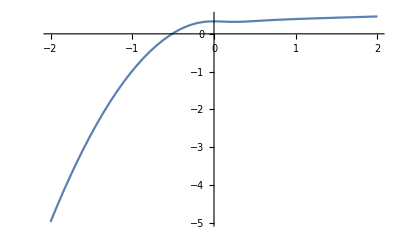

```mathematica
Plot[k1[x],{x,-2,2}]
```